### useful function

```mathematica
Load observable[file_]:=ToExpression[StringReplace[StringSplit[ReadString[file]],"e"->"*10^"]]
Plot mag[type_,D_,χ_]:=(files=Table[StringJoin[{"E:\\1 - research\\4.9 - AutoDiff\\data\\ADBCVUMPS\\K_J_Γ_Γ′_1x2\\K_J_Γ_Γ′{Float64}(-1.0, -0.1, 0.3, -0.02)_field[1.0, 1.0, 1.0]_",#1,"_",#2,"\\D",#3,"_χ",#4,"_observable.log"}&[ToString[NumberForm[i,{2,2}]],ToString[type],ToString[D],ToString[χ]]],{i,0.05,0.15,0.01}];
data=Load observable/@files;
ListPlot[Table[Table[{(i+4)/100,data[[i]][[j]]},{i,1,10}],{j,1,5}],PlotLegends->{mag,ferro,stripy,zigzag,Neel,etol,ΔE,Cross},Joined->Table[True,{i,1,6}],Mesh->All,PlotTheme->"Detailed",FrameLabel->{{None,None},{HoldForm["h"],None}},PlotLabel->HoldForm["E-h"],LabelStyle->{GrayLevel[0]}])
Plot ΔE[type_,D_,χ_]:=(files=Table[StringJoin[{"E:\\1 - research\\4.9 - AutoDiff\\data\\ADBCVUMPS\\K_J_Γ_Γ′_1x2\\K_J_Γ_Γ′{Float64}(-1.0, -0.1, 0.3, -0.02)_field[1.0, 1.0, 1.0]_",#1,"_",#2,"\\D",#3,"_χ",#4,"_observable.log"}&[ToString[NumberForm[i,{2,2}]],ToString[type],ToString[D],ToString[χ]]],{i,0.05,0.15,0.01}];
data=Load observable/@files;
ListPlot[Table[{(i+4)/100,data zigzag[[i]][[7]]},{i,1,16}],PlotLegends->ΔE,Joined->Table[True,{i,1,5}],Mesh->All,PlotTheme->"Detailed",FrameLabel->{{None,None},{HoldForm["h"],None}},PlotLabel->HoldForm["E-h"],LabelStyle->{GrayLevel[0]}])
```

### D=2

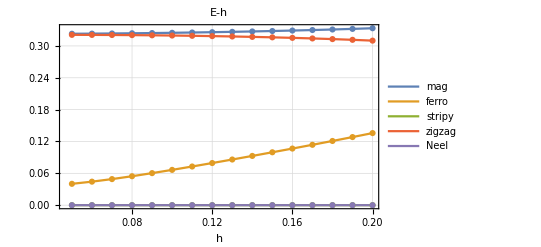

```mathematica
Plot mag[zigzag,2,20]
```

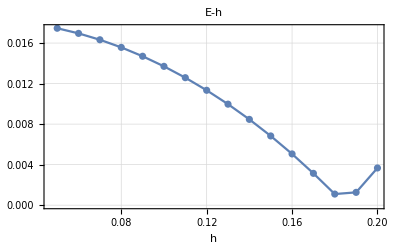

```mathematica
Plot ΔE[zigzag,2,20]
```

### D=4

```mathematica
Load observable[file_]:=ToExpression[StringReplace[StringSplit[ReadString[file]],"e"->"*10^"]]
Plot mag[type_,D_,χ_]:=(files=Table[StringJoin[{"E:\\1 - research\\4.9 - AutoDiff\\data\\ADBCVUMPS\\K_J_Γ_Γ′_1x2\\K_J_Γ_Γ′{Float64}(-1.0, -0.1, 0.3, -0.02)_field[1.0, 1.0, 1.0]_",#1,"_",#2,"\\observable.log"}&[ToString[NumberForm[i,{2,2}]],ToString[type]]],{i,0.05,0.20,0.01}];
data=Load observable/@files;
ListPlot[Table[Table[{(i+4)/100,data[[i]][[j]]},{i,1,16}],{j,1,5}],PlotLegends->{mag,ferro,stripy,zigzag,Neel,etol,ΔE,Cross},Joined->Table[True,{i,1,6}],Mesh->All,PlotTheme->"Detailed",FrameLabel->{{None,None},{HoldForm["h"],None}},PlotLabel->HoldForm["E-h"],LabelStyle->{GrayLevel[0]}])
Plot ΔE[type_,D_,χ_]:=(files=Table[StringJoin[{"E:\\1 - research\\4.9 - AutoDiff\\data\\ADBCVUMPS\\K_J_Γ_Γ′_1x2\\K_J_Γ_Γ′{Float64}(-1.0, -0.1, 0.3, -0.02)_field[1.0, 1.0, 1.0]_",#1,"_",#2,"\\observable.log"}&[ToString[NumberForm[i,{2,2}]],ToString[type],ToString[D],ToString[χ]]],{i,0.05,0.20,0.01}];
data=Load observable/@files;
ListPlot[Table[{(i+4)/100,data zigzag[[i]][[7]]},{i,1,16}],PlotLegends->ΔE,Joined->Table[True,{i,1,5}],Mesh->All,PlotTheme->"Detailed",FrameLabel->{{None,None},{HoldForm["h"],None}},PlotLabel->HoldForm["E-h"],LabelStyle->{GrayLevel[0]}])
```

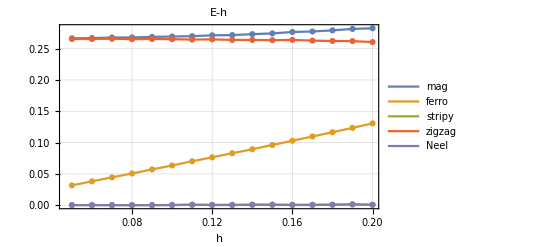

```mathematica
Plot mag[zigzag,4,80]
```

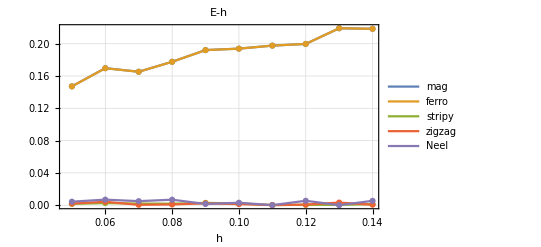

```mathematica
Plot mag[random,5,100]
```